1. Отделите графически корни алгебраического уравнения 
f (x) = 0 с помощью функции Plot . Найдите один из них (нецелый)  с точностью ξ= 10^-3 методом хорд . Укажите потребовавшееся число итераций . Проиллюстрируйте графически нахождение первых двух приближений (постройте график функции и хорды) .

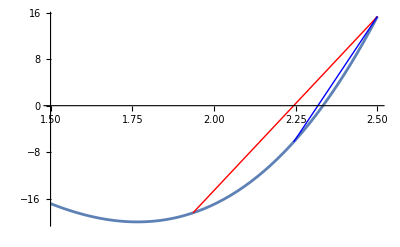

Root x = 2.33327, was acquired on 6 step.

```mathematica
f[x_] := 21*x^3-61*x^2+19*x+21
eps=10^(-3);
a = -1;
b = 2.5;
xPrev = 0;
counter = 0;
Plot[f[x], {x,a, b}, AxesOrigin->{0,0}, ImageSize-> Small]
While[(Abs[a-xPrev] >eps),
xPrev = a;
counter++;
a=a-(f[a]*(b-a)/(f[b]-f[a]));
If[counter == 2, Print[Plot[f[x], {x, 1.5, 2.5}, Epilog->{Red,Line[{{b,f[b]},{xPrev,f[xPrev]}}],Blue,Line[{{b,f[b]},{xNext,f[xNext]}}]}]]
];
];
Print["Root x = ", N[a], ", was acquired on ", counter, " step."]
```

2. Отделите графически и найдите с помощью функций Solve, NSolve, Roots, FindRoot корни алгебраического уравнения f (x) = 0. Разложите многочлен f (x) на множители, используя функцию Factor.

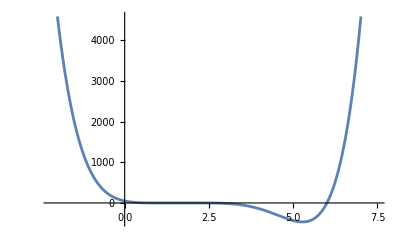

```mathematica
f[x_] := x^6 - 14 * x^5 + 73 * x^4 - 188 * x^3 + 256 * x^2 - 176 * x + 48
Plot[f[x], {x, -2.2, 7.5}]
```

```mathematica
Solve[f[x]==0]
```

{{x→1},{x→1},{x→2},{x→2},{x→2},{x→6}}

```mathematica
NSolve[f[x]==0]
```

{{x→1.},{x→1.},{x→2.},{x→2.},{x→2.},{x→6.}}

```mathematica
Roots[f[x] == 0, x]
```

x==1||x==1||x==2||x==2||x==2||x==6

```mathematica
FindRoot[f[x]==0,{x,6}]
```

{x→6.}

```mathematica
Factor[f[x]]
```

(-6+x) (-2+x)^3 (-1+x)^2

Как видно, данное уравнение имеет три корня, причем корни 1 и 2
являются двукратным  и трехкратным корнями соответственно

3. Отделите графически корни трансцендентного уравнения с помощью функции Plot. Найдите один из них  с точностью ξ= 10^-3 : а) методом Ньютона; б) методом секущих. Укажите потребовавшееся число итераций
a)

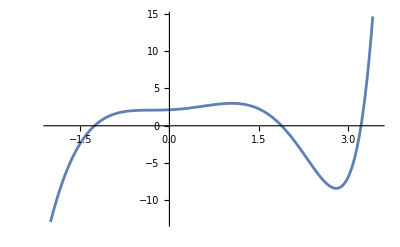

Решение x=-1.26082 получено на 4  шаге.

```mathematica
f[x_] := 7^(x-1) + 3^x - x ^4 - x + 1
b = -1;
eps = 10^-3;
x1 = b;
Plot[f[x], {x, -2, 3.5}]
Do[x2 = x1; x1 = (x1 - f[x1]/f'[x1])//N;
If[Abs[x2-x1]<eps, Print["Решение x=", x2//N, " получено на ", n " шаге."];
Break[]],{n,1,100}]
```

b)

```mathematica
f[x_] := 7^(x-1) + 3^x - x ^4 - x + 1
b = -1;
eps = 10^-3;
x1 = b;
x3 = x1;
x1 = (x1 - f[x1]/f'[x1]);
Plot[f[x], {x, -2, 3.5}]
Do[x2 = x1; x1 = x1-((x1 - x3)* f[x1]/(f[x1]-f[x3]))//N;x3 = x2;
If[Abs[x2-x1]<eps, Print["Решение x=", x2//N, "получено на ", n " шаге."];
Break[]],{n,1,100}]
```

-Graphics-

Решение x=-1.26085получено на 4  шаге.

4. Приведите уравнение (3.1 – 3.16) к виду, пригодному для итераций. Найдите его корни методом простых итераций  с точностью ξ= 10^-3 
 Укажите потребовавшееся число итераций.

```mathematica
f[x_]:= 7^(x-1) + 3^x - x ^4 - x + 1
a=-2;
b = -1;
eps = 10^-3;
x1 = b;
f2[x_] = f'[x];
Plot[f[x], {x, -2, 3.5}]
Do[x2 = x1;  λ = 1/f2[x1]; x1 = x1 - λ*f[x1];
If[Abs[x2-x1]<eps, Print["Решение x=", x2//N, "получено на ", n " шаге."];
Break[]],{n,1,100}]
```

-Graphics-

Решение x=-1.26082получено на 4  шаге.

5. Решите уравнение (3.1 – 3.16) с помощью функций Solve, NSolve, FindRoot.

```mathematica
f[x_]:= 7^(x-1) + 3^x - x ^4 - x + 1
```

```mathematica
Solve[f[x]==0 && -10<x<10,x]
```

{{x→Root-1.26Root[{-7-7 3^#1-7^#1+7 #1+7 #1^4&,-1.2603207145756552568}]-1.2603207145756552},{x→Root1.89Root[{-7-7 3^#1-7^#1+7 #1+7 #1^4&,1.8871785237009854064}]1.8871785237009855},{x→Root3.22Root[{-7-7 3^#1-7^#1+7 #1+7 #1^4&,3.2231920440382522131}]3.223192044038252}}

```mathematica
NSolve[f[x]==0 && -10<x<10,x]
```

{{x→-1.26032},{x→1.88718},{x→3.22319}}

```mathematica
FindRoot[f[x]==0,{x,4}]
```

{x→3.22319}

6. Дана система двух нелинейных уравнений f (x, y)= 0 , g(x, y)= 0. Используя средства пакета Mathematica, изобразите на одном чертеже кривые f (x, y) =0 и g(x, y)= 0 , и решите данную систему.

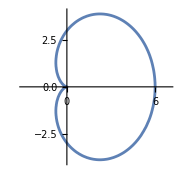

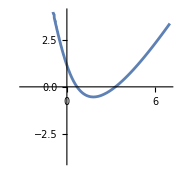

```mathematica
f[x_,y_] := (x^2 + y^2 - 3*x)^2 - 9*(x^2 + y^2)
g[x_,y_] := 2*y - 3 * x + 5 * Log[4*x + y] - 3
gr1 = ContourPlot[f[x,y]== 0, {x,-3,7},{y,-4,4},Axes -> True, Frame -> False, ImageSize -> Small]
gr2 = ContourPlot[g[x,y]== 0, {x,-3,7},{y,-4,4},Axes -> True, Frame -> False, ImageSize -> Small]
```

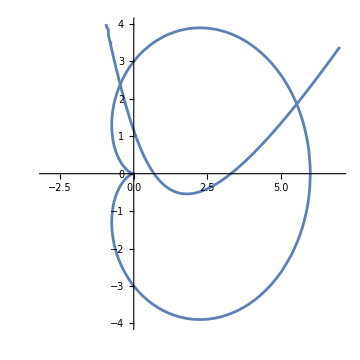

```mathematica
Show[gr1, gr2, ImageSize -> Medium]
```

```mathematica
FindRoot[{f[x,y]==0, g[x,y]==0}, {x,0}, {y,2}]
```

{x→-0.462892,y→2.38354}

```mathematica
FindRoot[{f[x,y]==0, g[x,y]==0}, {x,6}, {y,2}]
```

{x→5.53919,y→1.86172}